```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model -> "./modelFiles/SMS-stop_FA/SMS-stop_FA"];
```

```mathematica
processDMEFT = { V[4],V[4]} -> {F[13],F[13]};
nameDMEFT = "DM-EFT";
topsDMEFT = CreateTopologies[1, 2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
insDMEFT = InsertFields[topsDMEFT, processDMEFT,InsertionLevel-> {Particles},ExcludeParticles->{S[1]}];
FR$ClassesTranslation
```

generic model {Lorentz} initialized

classes model {./modelFiles/SMS-stop_FA/SMS-stop_FA} initialized

in total: 18 Particles insertions

{A→V(1),Z→V(2),W→V(3),G→V(4),ghA→U(1),ghZ→U(2),ghWp→U(3),ghWm→U(4),ghG→U(5),ve→F(1),vm→F(2),vt→F(3),e→F(4),mu→F(5),ta→F(6),u→F(7),c→F(8),t→F(9),d→F(10),s→F(11),b→F(12),H→S(1),G0→S(2),GluonPropagator→S(3),chi→F(13),ST→S(4)}

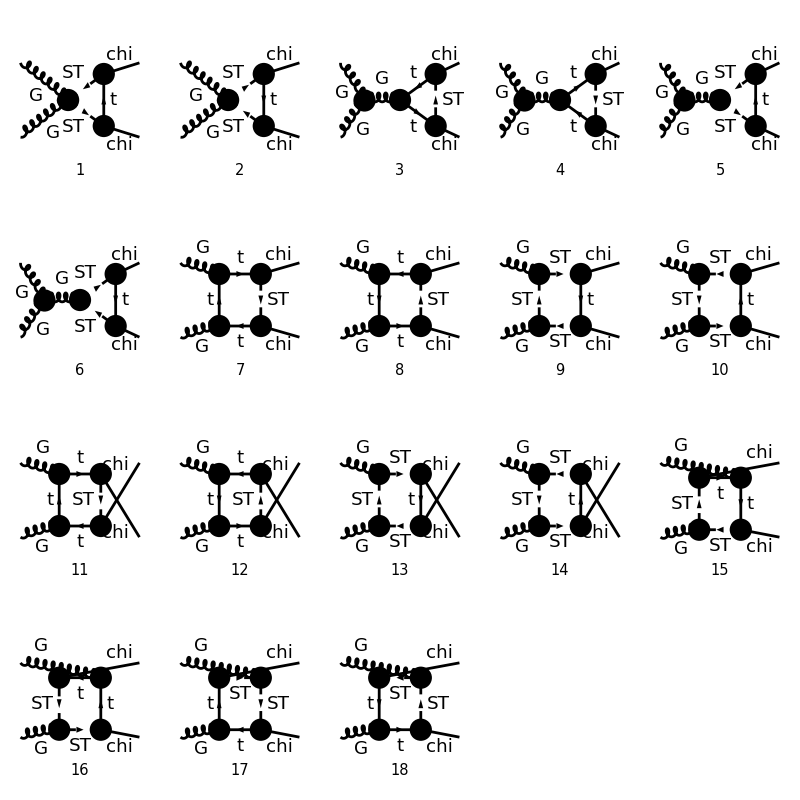

```mathematica
Paint[insDMEFT,ColumnsXRows->{5,4},PaintLevel->{Particles},ImageSize->{800,800},Numbering->Simple];
```

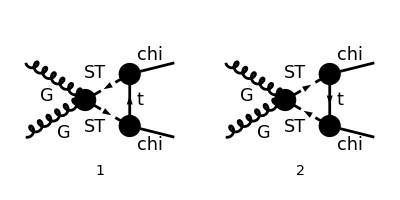

```mathematica
diags=DiagramExtract[insDMEFT,{1,2}];
Paint[diags,ColumnsXRows->{2,1},ImageSize->{400,200},Numbering->Simple];
```

```mathematica
(* Set Truncated->True to remove external fields  *)
amp[0]=FCFAConvert[CreateFeynAmp[diags,PreFactor->1,Truncated->True],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},List->False,TransversePolarizationVectors->{p1,p2},DropSumOver->True,SMP->True,List->False,LorentzIndexNames-> {μ,ν,σ,ρ},Contract->False,FinalSubstitutions-> M$FACouplings,ChangeDimension->D,UndoChiralSplittings->True]
```

in total: 2 Particles amplitudes

(GS^2 g^μν ((T^Glu1 T^Glu2)_Col5Col5+(T^Glu2 T^Glu1)_Col5Col5) (-ⅈ yDM (γ̄)^6).(MT+γ·q).(-ⅈ yDM (γ̄)^7))/((q^2-MT^2).((k1+q)^2-mST^2).((q-k2)^2-mST^2))+(GS^2 g^μν ((T^Glu1 T^Glu2)_Col5Col5+(T^Glu2 T^Glu1)_Col5Col5) (-ⅈ yDM (γ̄)^7).(MT+γ·q).(-ⅈ yDM (γ̄)^6))/((q^2-MT^2).((k1+q)^2-mST^2).((q-k2)^2-mST^2))

```mathematica
FCClearScalarProducts[];
ScalarProduct[k1,k1]=mChi^2;
ScalarProduct[k2,k2]=mChi^2;
ScalarProduct[p1,p1]=0;
ScalarProduct[p2,p2]=0;
ScalarProduct[k1,k2]=s/2;
```

```mathematica
amp[1]=SUNSimplify[FCTraceFactor[amp[0]]]
```

-(GS.GS yDM^2 g^μν δ^Glu1Glu2 ((γ̄)^6.(MT+γ·q).(γ̄)^7+(γ̄)^7.(MT+γ·q).(γ̄)^6))/((q^2-MT^2).((k1+q)^2-mST^2).((k2-q)^2-mST^2))

```mathematica
amp[2]=FullSimplify[DiracSimplify[amp[1]]]
```

-(GS.GS yDM^2 g^μν δ^Glu1Glu2 ((γ·q).(γ̄)^6+(γ·q).(γ̄)^7))/((q^2-MT^2).((k1+q)^2-mST^2).((k2-q)^2-mST^2))

```mathematica
amp[3]=TID[amp[2],q,UsePaVeBasis->True]//Simplify
```

-ⅈ π^2 GS.GS yDM^2 g^μν δ^Glu1Glu2 ((γ·(k1-k2)).(γ̄)^6+(γ·(k1-k2)).(γ̄)^7) C_1(mChi^2,2 mChi^2+s,mChi^2,MT^2,mST^2,mST^2)

```mathematica
amp[4]=PaVeReduce[amp[3]]//Simplify
```

1/(2 mChi^2-s)ⅈ π^2 GS.GS yDM^2 g^μν δ^Glu1Glu2 ((γ·(k1-k2)).(γ̄)^6+(γ·(k1-k2)).(γ̄)^7) (-B_0(mChi^2,mST^2,MT^2)+B_0(2 mChi^2+s,mST^2,mST^2)+(mChi^2-mST^2+MT^2) C_0(mChi^2,mChi^2,2 mChi^2+s,mST^2,MT^2,mST^2))

```mathematica
amp[4]=Simplify[PaXEvaluate[amp[3],PaXC0Expand->False,PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)],Assumptions-> {s^2 > 4 Subscript[m, χ]^2}]
```

PaXEvaluate::C0D0: The explicit result for the occurring C0 function(s) is expected to be very complicated. Please rerun PaXEvaluate with the option PaXC0Expand->True to show the result nevertheless. Please set $FCAdvice=False if you do not want to see this message in future.

1/(32 π^2 m_χ^2 (4 m_χ^4-s^2))ⅈ GS.GS yDM^2 g^μν δ^Glu1Glu2 ((γ·k1).(γ̄)^6-(γ·k2).(γ̄)^6) (2 m_χ^2 (m^2+m_χ^2-M^2) (2 m_χ^2+s) C_0(m_χ^2,m_χ^2,s+2 m_χ^2,M^2,m^2,M^2)+s m_χ^2 log(m^2/M^2)-2 s √(-2 (m^2+M^2) m_χ^2+(m^2-M^2)^2+m_χ^4) log((√(-2 (m^2+M^2) m_χ^2+(m^2-M^2)^2+m_χ^4)+m^2-m_χ^2+M^2)/(2 m M))+m^2 s log(m^2/M^2)-M^2 s log(m^2/M^2)+2 m_χ^4 log(m^2/M^2)+2 m^2 m_χ^2 log(m^2/M^2)-2 M^2 m_χ^2 log(m^2/M^2)-4 m_χ^2 √(-2 (m^2+M^2) m_χ^2+(m^2-M^2)^2+m_χ^4) log((√(-2 (m^2+M^2) m_χ^2+(m^2-M^2)^2+m_χ^4)+m^2-m_χ^2+M^2)/(2 m M))+2 m_χ^2 √((2 m_χ^2+s) (2 m_χ^2-4 M^2+s)) log((√((2 m_χ^2+s) (2 m_χ^2-4 M^2+s))-2 m_χ^2+2 M^2-s)/(2 M^2)))

```mathematica
Quit[];
```

```mathematica
Needs["X`"]
```

Package-X v2.1.1, by Hiren H. Patel
For more information, see the

```mathematica
amp[0]=PVC[0,1,0,mc^2, 2 mc^2 + s,mc^2,m,M,M]
```

C_1(mc^2,2 mc^2+s,mc^2;m,M,M)

```mathematica
LoopRefine[amp[0],Part-> UVDivergent]
```

0

```mathematica
amp[1]=LoopRefine[amp[0]]//DiscExpand//FullSimplify
```

-(2 (m^2-M^2+mc^2) C_0(mc^2,mc^2,2 mc^2+s;M,m,M)-(2 λ^(1/2)(m^2,M^2,mc^2) log((λ^(1/2)(m^2,M^2,mc^2)+m^2+M^2-mc^2)/(2 m M)))/mc^2+((m^2-M^2+mc^2) log(m^2/M^2))/mc^2+(2 √((2 mc^2+s) (-4 M^2+2 mc^2+s)) log((√((2 mc^2+s) (-4 M^2+2 mc^2+s))+2 M^2-2 mc^2-s)/(2 M^2)))/(2 mc^2+s))/(2 (2 mc^2-s))

```mathematica
amp[2]=FullSimplify[amp[1]/.{s-> (Subscript[a, s] M)^2,mc-> Subscript[a, c] M,m-> Subscript[a, t] M},Assumptions->{M>0,Subscript[a, s]>0,Subscript[a, c]>0,Subscript[a, t]>0}]
```

-1/(M^2 (2 (a^c)^2-(a^s)^2))((((a^c)^2+(a^t)^2-1) (M^2 (a^c)^2 C_0(M^2 (a^c)^2,M^2 (a^c)^2,M^2 (2 (a^c)^2+(a^s)^2);M,M a^t,M)+log(a^t)))/((a^c)^2)+(λ^(1/2)(M^2,M^2 (a^c)^2,M^2 (a^t)^2) (-log(λ^(1/2)(M^2,M^2 (a^c)^2,M^2 (a^t)^2)+M^2 (-(a^c)^2+(a^t)^2+1))+log(a^t)+2 log(M)+log(2)))/(M^2 (a^c)^2)+√(1-4/(2 (a^c)^2+(a^s)^2)) log(1/2 (√((2 (a^c)^2+(a^s)^2-4) (2 (a^c)^2+(a^s)^2))-2 (a^c)^2-(a^s)^2+2)))

```mathematica
amp0=FullSimplify[Normal[LoopRefineSeries[amp[2],{Subscript[a, s],0,1},{Subscript[a, t],0,1},{Subscript[a, c],0,1}]],Assumptions->{M>0,Subscript[a, s]>0,Subscript[a, c]>0,Subscript[a, t]>0}]
```

7/(12 M^2)

```mathematica
amp1=FullSimplify[Normal[LoopRefineSeries[amp[2],{Subscript[a, s],0,1},{Subscript[a, t],0,1}]],Assumptions->{M>0,Subscript[a, s]>0,Subscript[a, c]>0,Subscript[a, t]>0,Subscript[a, c]<1}]
```

-(M^2 ((a^c)^2-1) (a^c)^2 C_0(M^2 (a^c)^2,M^2 (a^c)^2,2 M^2 (a^c)^2;M,M a^t,M)+√((a^c)^2-2) a^c log(a^c (√((a^c)^2-2)-a^c)+1)+((a^c)^2-1) log(1-(a^c)^2))/(2 M^2 (a^c)^4)